# 第7章 在Mathematica中作图

## §7 .1 二维图形

### 1. 一元函数作图

Plot[f, {x, xmin, xmax}] 画出函数f在[xmin, xmax] 的图形

Plot[{f1, f2, …}, {x, xmin, xmax}] 将多个函数画在一起

Plot[…, {x} ∈ reg] x 从几何区域 reg 取值

Plot[{.85,w[fi],厎,.85]  绘制 fi ，其特征由符号封装 w 所定义.

```mathematica
Plot[Tan[x],{x,-3,3}]
```

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 Pi},PlotLegends->"Expressions"]
```

例题 用区域表示自变量取值范围

```mathematica
reg1=ImplicitRegion[-2Pi≤x≤-1∨1≤x≤2Pi,{x}]
Plot[Sin[2 x],x∈reg1]
```

```mathematica
reg2=MeshRegion[{{-2},{-1},{-1/2},{1/2},{1},{2}},Line[{{1,2},{3,4},{5,6}}]];
Plot[x^2+3x,x∈reg2]
```

Plot[Evaluate[f], {x, xmin, xmax}]

（1） f是一个生成函数表的命令时，用户想要 Mathematica 先生成这个表，然后计算函数值.

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10}]
```

（2） 当f不是显式表达式时，可用 Evaluate 绘图函数取值。

```mathematica
Plot[Evaluate[Integrate[Sin[x]Cos[2x],x]],{x,0,5}]
```

### 以下封装 w 可用于 fi：

Annotation[fi, label]        为 fi 提供注释

Button[fi, action]              当点击 fi 曲线时，执行 action

Callout[fi, label, pos]      在相对位置 pos 上放置 callout

Hyperlink[fi, uri]                将函数变为超链接

Labeled[fi, label, pos]     在相对位置 pos 上放置标签

Legended[fi, label]           在图例中标识函数

PopupWindow[fi, cont]  为函数添加弹出窗口

StatusArea[fi, label]         当鼠标移过时在状态栏中显示

Style[fi, styles]                  用指定样式显示函数

Tooltip[fi, label]              在函数上附加提示条

点击图像时获取点的坐标

```mathematica
Plot[{Button[Sin[x],Print[MousePosition["Graphics"]]],Cos[x]},{x,-Pi,Pi}]
```

在函数上附加提示条

```mathematica
Plot[{Tooltip[Sin[x],.94sin(x).94],Cos[x]},{x,-Pi,Pi}]
```

给曲线附加超链接

```mathematica
Plot[{Hyperlink[Sin[x], "Http://reference.wolfram.com/language/ref/Hyperlink.html"],Cos[x]},{x,-Pi,Pi}]
```

标注曲线，曲线图例

```mathematica
ListPlot[Table[Labeled[Prime[i],{Prime[i]},Above],{i,15}]]
```

```mathematica
Plot[{Legended[Sin[x],"sin(x)"],Legended[Cos[x],"cos(x)"]},{x,-Pi,Pi}]
```

弹出窗口

```mathematica
Plot[{PopupWindow[Sin[x],  Graphics[Circle[]]], Cos[x]},{x,0,2Pi}]
```

### 2. 作图函数的选项设置

Mathematica 绘图时，需要进行许多选择.必须规划出绘图的比例，函数采样的地方，画坐标轴的方式等等.大多数情况下，Mathematica 会作出相当好的选择.但是，如果用户为了特殊的目的想要得到最好的图形，那么用户必须帮助 Mathematica 作出某些选择。

Plot[f, {x, xmin, xmax}, option -> value]，绘图，为某个选项指定特定值

选项                               默认值                   说明

AspectRatio              1/GoldenRatio         绘图的高宽比，   Automatic 表示自动根据x 和 y 坐标绝对值进行设置

Axes                             True                          是否包括坐标轴

AxesLabel                  None                         贴在轴上的标签，ylabel 指定y 轴标签，{xlabel, ylabel} 指定两轴标签

Filling                          None                         插入每个曲线下的填充

FillingStyle                 Automatic                用于填充的样式

Frame                          False                         是否在绘图周围加画框

FrameLabel               None                         框架周围要贴的标签，从下x 轴开始按顺时针顺序给出列表

MaxRecursion           Automatic                允许的最大递归细分数

Mesh                           None                          在每条曲线上绘制多少个网格点

MeshFunctions        {#1 &}                          如何决定网格点的放置位置

MeshShading           None                          怎样处理网格点之间区域的色调

MeshStyle                 Automatic                 网格点的样式

Method                      Automatic                 修饰曲线的方法

PlotLabel                  None                           整个绘图的标签

PlotLabels                None                           曲线的标签

PlotLayout	      Automatic	              曲线位置排列

PlotLegends            None                            曲线的图例

PlotPoints                Automatic                   采样函数的初始点数

PlotRange                {Full, Automatic}        y 的范围或要包含的其他值

PlotStyle                  Automatic                   指定每条曲线样式的图形指令

PlotTheme              $PlotTheme                绘图的整体外观主题

RegionFunction     (True &)                        如何确定是否应包含一个点

ScalingFunctions  None                             如何缩放个别坐标

TargetUnits            Automatic                    在绘图中显示的单位

WorkingPrecision MachinePrecision       内部计算使用的精度

例题：常用选项示例

(1)曲线光滑程度

```mathematica
Table[Plot[Sin[x], {x, 0, 15}, PlotPoints -> pp,   MaxRecursion -> mr], {mr, {0, 1, 2}}, {pp, {5, 10, 15}}]
```

(2) 显示图例

```mathematica
Plot[{Cos[x],Sin[2 x],Cos[3 x]},{x,0,2 Pi},PlotLegends->"Expressions"]
```

（3） 标注每条曲线，PlotLabels,   Labeled ，Callout"数据绘制标签"

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},PlotLabels->"Expressions"]
Plot[{Labeled[Cos[x],cos[x]],Labeled[Sin[x],sin[x]]},{x,0,2 Pi}]
Plot[Labeled[Sin[x],"sin(x)",3],{x,0,2Pi}] (*在x=3附近加标签*)
Plot[Labeled[Sin[x],Sin[x],{Scaled[0.8],Above}],{x,0,2Pi}] (*在x=0.8*2Pi处曲线上方加标签*)
```

Callout[data, expr, pos]在由 pos 指定的位置处显示标注 expr.

```mathematica
Plot[Labeled[x^Sin[x],x^Sin[x],{Scaled[0.2],Right}],{x,0,2Pi}]
```

PlotLabel 图片整体的 "绘图标签"

```mathematica
Table[Plot[Labeled[Sin[x],f[x],p],{x,0,2 Pi},PlotLabel->p],{p,{Above,Below,Before,After}}]
```

(4) 给图形加上框线和网格

```mathematica
Plot[Sin[x^2],{x,0,3},Frame->True,GridLines->Automatic]
```

(5) 填充曲线，坐标轴之间区域

```mathematica
Plot[Sin[2 x],{x,0,2 Pi},Filling->Axis]
Plot[Cos[x],{x,0,Pi},Filling->Bottom]
Plot[Cos[x],{x,0,Pi},Filling->Top]
```

(6) 填充两条曲线之间的区域

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x,Sin[x]+2x},{x,0,10},Filling->{1->{2},2->{3}}]
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.1],Blue]]
```

(7) 绘图范围

```mathematica
Plot[Log[x],{x,-1,5},PlotRange->Full]
Plot[Log[x],{x,-1,5},PlotRange->Automatic]
Plot[Log[x],{x,-1,5},PlotRange->1]
```

(8) 曲线颜色 ColorFunction
 GrayLevel[ i ]                    0(黑)和 1(白)之间的灰度
 RGBColor[ r , g , b ]        用 0 与 1 指定红、绿、兰分量的颜色
Hue[ h ]                             色度值 h 在 0 和 1 之间的颜色
Hue[ h ，b， l ]             色度、饱和度和亮度值在 0 和 1 之间的颜色

```mathematica
Plot[Sin[x],{x,0,10},ColorFunction->"DarkRainbow"]
Plot[Sin[x],{x,0,10},ColorFunction->Function[{x,y},If[y>0,Red,Black]],ColorFunctionScaling->False,PlotStyle->Thick]
```

```mathematica
{Plot[Sin[x],{x,0,10},ColorFunction->Function[{x,y},Hue[y]]],Plot[Sin[x],{x,0,10},ColorFunction->Function[{x,y},Hue[x]]]}
```

(9) 在所得的图形中插入图形对象

```mathematica
Plot[Sin[x],{x,0,4 Pi},Epilog->{PointSize[0.04],Point[{0,0}],Point[{Pi,0}],Point[{2 Pi,0}],Point[Table[{k Pi,Sin[k Pi]},{k,0.5,4,1}]]}]
```

```mathematica
Plot[Floor[x],{x,-2,3}]
Plot[Floor[x],{x,-2,3},Epilog->{Table[Disk[{i,i},Offset[2.]],{i,-2,2}],Table[{EdgeForm[Black],White,Disk[{i+1,i},Offset[2]]},{i,-2,2}]}]
```

例题：Plotstyle选项示例

PlotStyle -> {g1, g2, …} 指定连续指令 gi 应该循环用于连续对象.
    PlotStyle 可以应用于点，线和面.

PlotStyle -> None 指定不直接绘制图形中的主要对象，但网格和填充不受影响

Dashing[{w1, …}]   指定虚线                                       EdgeForm[g]绘制边的规范

FaceForm[g]绘制面的规范                                         Glow[c]发光

GrayLevel[i]灰度[0, 1]                                                   Opacity[a]不透明度[0, 1]

PointSize[d]点的大小                                                  Directive[g1, g2, …]图形指令组合

Red, Blue, 等.已命名的颜色                                      RGBColor[r, g, b]RGB 色[0, 1]

Specularity[s]表面的反射                                          Thickness[w]线的粗细 << 1

```mathematica
Plot[Evaluate@Table[BesselJ[n,x],{n,3}],{x,0,15},PlotStyle->{Orange,Dashed,Thickness[0.01]}]
```

对曲线着色，ColorFunction 比 PlotStyle 有更高的优先级

```mathematica
Plot[Sinc[x],{x,0,10},ColorFunction->"DarkRainbow",PlotStyle->Directive[Red,Thick]]
```

### 2. 二维参数作图

ParametricPlot[{fx, fy}, {u, umin, umax}]
产生一个曲线的参数图，其中 x 和 y 的坐标 fx 和 fy 为 u 的函数.

ParametricPlot[{{fx, fy}, {gx, gy}, …}, {u, umin, umax}] 绘制几个参数曲线.

ParametricPlot[{fx, fy}, {u, umin, umax}, {v, vmin, vmax}] 绘制一个参数区域.

ParametricPlot[{{fx, fy}, {gx, gy}, …}, {u, umin, umax}, {v, vmin, vmax}]
绘制几个参数区域.

ParametricPlot[…, {u, v} ∈ reg] 从几何区域 reg 中取得参数 {u, v}.

ParametricPlot[{.85,w[{fx,fy}],...,.85]绘制特征由符号封装 w 定义的曲线 {fx,fy}

```mathematica
ParametricPlot[{Cos[t]^3,Sin[t]^3},{t,0,2Pi}]
```

```mathematica
ParametricPlot[{r Cos[t]^3,r Sin[t]^3},{t,0,2 Pi},{r,0,1}]
```

```mathematica
ParametricPlot[{{3 Cos[t],3 Sin[t]},{3 Cos[t],Sin[t]},{Cos[t],3Sin[t]},{Cos[t],Sin[t]}},{t,0,2 Pi},PlotLegends->"Expressions"]
```

参数属于某区域

```mathematica
reg3=MeshRegion[{{0,1},{2,4},{5,2}},Polygon[{1,2,3}]]
ParametricPlot[r^2 {Sqrt[t] Cos[t],Sin[t]},{t,r}∈reg3]
```

在函数值变化较快的位置，用更多的样本点

```mathematica
ParametricPlot[{Sin[12 u] Cos[u],Sin[12 u] Sin[u]},{u,0,2 Pi}]
```

选项与Plot函数类似

```mathematica
ParametricPlot[{u Cos[u],u Sin[u]},{u,0,2 Pi},PlotLabels->"Expressions"]
```

```mathematica
ParametricPlot[{{u Cos[u],u Sin[u]},{2 u Cos[u],2 u Sin[u]},{3 u Cos[u],3 u Sin[u]}},{u,0,3/2 Pi},PlotLabels->Callout["Expressions",After]]
```

```mathematica
ParametricPlot[{{u Cos[u],u Sin[u]} (t-u),{2 u Cos[u],2 u Sin[u]} (t-u),{3 u Cos[u],3 u Sin[u]} (t-u)},{u,0,2 Pi},{t,0,1},PlotLegends->"Expressions"]
```

```mathematica
ParametricPlot[{(u+v) Cos[u],(u+v) Sin[u]},{u,0,4 Pi},{v,0,5},BoundaryStyle->Red,Mesh->None]
```

### 3. 隐函数表示的曲线

ContourPlot[f == g, {x, xmin, xmax}, {y, ymin, ymax}, 可选项]        绘制 f = g 的等高线

ContourPlot[{f1 == g1, f2 == g2, …}, {x, xmin, xmax}, {y, ymin, ymax}]         绘制多个等高线.

ContourPlot[…, {x, y} ∈ reg]将变量 {x, y} 选在几何区域 reg 中.

例题 : 绘制隐函数 : x^4 + y^4 - 2 (x^2 + y^2) + 1 = 0 在区间一 3 < x < 3, -3 < y < 3 上的图形.

```mathematica
ContourPlot[x^4+y^4-2(x^2+y^2)+1==0,{x,-3,3},{y,-3,3}]
```

```mathematica
ContourPlot[x^2-y^2==x^3,{x,-2,2},{y,-2,2}]
```

### 4. 极坐标表示的曲线

PolarPlot[r, {θ, θmin, θmax}] 产生一个半径为 r 的曲线极坐标图，作为角度 θ 的函数.

PolarPlot[{r1, r2, …}, {θ, θmin, θmax}] 产生一个曲线的极坐标，显示径函数 r1，r2，….

```mathematica
PolarPlot[Sin[10 t],{t,0,Pi}]
PolarPlot[{1,1+1/10 Sin[20 t]},{t,0,2 Pi},PlotStyle->{Green,Directive[Dashed,Thick,Orange]}]
```

可选项与Plot函数类似.

```mathematica
PolarPlot[Callout[Sqrt[t],Sqrt[t],Scaled[0.8]],{t,0,2 Pi}]
PolarPlot[Sqrt[t],{t,0,2 π},Axes->{True,False}]

PolarPlot[Sin[4 θ],{θ,0,2 Pi},ColorFunction->"DarkRainbow",PlotStyle->Directive[Red,Thick]]

PolarPlot[Sin[4 θ],{θ,0,2 Pi},ColorFunction->Function[{x,y,t,r},If[t>Pi,Red,Black]],ColorFunctionScaling->False,PlotStyle->Thick]
```

### 5. 重现和组合图形

Show[plot, option -> value] 改变选项重画图形

Show[plot1, plot2, …] 将若干图形画在一起

GraphicsGrid[{{plot1, plot2, …}, …}] 画图形列阵

GraphicsRow[{plot1, plot2, …}] 在一行画几个图形

GraphicsColumn[{plot1, plot2, …}] 在一列画几个图形

修改图形

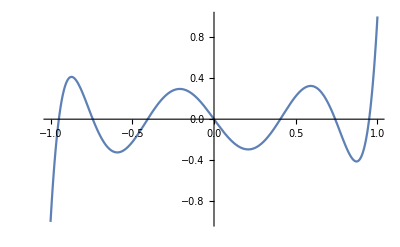

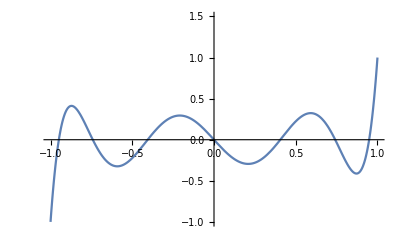

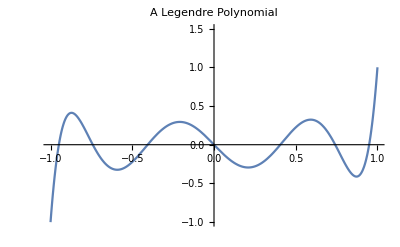

```mathematica
g0=Plot[LegendreP[7,x],{x,-1,1}]
Show[%,PlotRange->{-1,1.5}]
Show[%,PlotLabel->"A Legendre Polynomial"]
```

Wolfram 语言的所有图形都是表达式，起操控方式与其他表达式相同.这些操控不要求使用 Show.

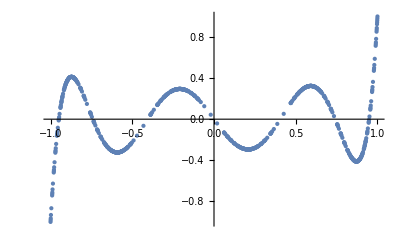

```mathematica
g0/.Line->Point
```

```mathematica
（2）组合图形
```

```mathematica
g1=Plot[x^2-9,{x,-2,5},PlotStyle->{Dashed,Red,Thick}]
g2=Plot[10Sin[x],{x,0,2Pi},PlotStyle->Yellow]
g3=Show[g1,g2]
```

```mathematica
图形范围与g1保持一致，完全显式可以修改为
```

```mathematica
g3=Show[g1,g2,PlotRange->All]

g4=Plot[BesselJ[0,x],{x,0,10}]
g5=Plot[BesselY[1,x],{x,1,10}]

g6=Show[g4,g5]
```

```mathematica
GraphicsGrid[{{g1,g2,g3},{g4,g5,g6}}]
GraphicsRow[{g3,g6}]
```

### 6. 二维数据绘图

ListPlot[{y1, …, yn}] 绘制点 {1, y1}, {2, y2}, ….

ListPlot[{{x1, y1}, …, {xn, yn}}] 为坐标为 {xi, yi} 的点生成二维散点图.

ListPlot[数据, Joined -> True] 画一条通过数据点的折线

ListLinePlot[{{xl，yl}，{x2，y2}，…}] 按选项连接数据点

List PolarPlot[data] 在极坐标系下画离散点列 data

```mathematica
y=RandomReal[{-1,1},100]
```

```mathematica
ListPlot[y]
```

```mathematica
ListPlot[y,Joined->True]
```

```mathematica
ListPlot[Table[{Sin[n],Sin[2 n]},{n,50}]]
```

```mathematica
ListPlot[Table[{x,Sin[x]},{x,0,2 Pi,0.1}],Filling->Axis,PlotLegends->{"Sin x"}]
```

```mathematica
ListPlot[Labeled[#,#]&/@Table[Prime[n],{n,10}],PlotStyle->PointSize[Medium]]
```

按顺序链接各点

```mathematica
ListLinePlot[Table[{Cos[k 2 Pi/7],Sin[k 2 Pi/7]},{k,0,21,3}],Frame->True,Axes->False]
```

```mathematica
ListPlot[Table[{Cos[k 2 Pi/7],Sin[k 2 Pi/7]},{k,0,21,3}],Joined->True,Frame->True,Axes->False]
```

## §7 .2 三维图形

### 1. 二元函数作图

Plot3D[f, {x, xmin, xmax}, {y, ymin, ymax}, 可选项] 产生函数 f 在 x 和 y 上的三维图形

Plot3D[{f1, f2, …}, {x, xmin, xmax}, {y, ymin, ymax}, 可选项] 绘制几个函数.

Plot3D[…, {x, y} ∈ reg, 可选项] 变量 {x, y} 从几何区域 reg 取值.

Plot3D[{…,w[fi],…},…] 绘制特征由符号封装 w 定义的 fi.

```mathematica
Plot3D[Sin[x+y],{x,-3,3},{y,-2,2}]
```

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2+9},{x,-2,2},{y,-2,2}]
```

```mathematica
reg=ImplicitRegion[x^2+y^2≤15,{x,y}];
Plot3D[{x^2+y^2,-x^2-y^2+9},{x,y}∈reg]
```

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2+9},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2≤15]]
```

自变量的区域可以先定义好，也可以在Plot3D函数中用隐函数说明.

### 封裝函數

Annotation[fi, label] 为 fi 提供注解

Button[fi, action] 当点击曲线 fi 时计算 action

Callout[fi, label, pos] 把标注放在相关位置 pos

EventHandler[fi, events] 为 fi 定义一般事件句柄

Hyperlink[fi, uri] 使函数成为超链接

Labeled[fi, label, pos] 把标签放在相关位置 pos

Legended[fi, label] 在图例中标识函数

PopupWindow[fi, cont] 把弹出窗口附加在函数中

StatusArea[fi, label] 鼠标悬停时显示在状态区域

Style[fi, styles] 使用指定的样式显示函数

Tooltip[fi, label] 把提示条附加在函数上

选项                     默认值	                 说明

Axes                              True                                     是否绘制轴

BoundaryStyle         Automatic                          如何绘制曲面的边界线

BoxRatios                   {1, 1, 0.4}	                     有界 3 D box 比例

ClippingStyle            Automatic                          如何绘制曲面的剪切部分

ColorFunction          Automatic                          如何决定曲面的颜色

EvaluationMonitor  None                                    在每次函数计算时需要计算的表达式

Exclusions                  Automatic                          排除的 x、y 曲线

ExclusionsStyle        None                                    如何绘制排除曲线

Filling                           None                                    每个曲面下的填充

FillingStyle                 Opacity[0.5]                       填充使用的样式

MaxRecursion            Automatic                         递归子划分的最大数量

Mesh                             Automatic                         每个方向上绘制网格线的数量

MeshShading             None                                   如何设置网格线之间的阴影区域

MeshStyle                   Automatic                         网格线的样式

PlotLabels                  None                                   用于曲面的标签

PlotLegends               None                                   曲面的图例

PlotPoints                  Automatic                          每个方向上样本点的最初数量

PlotRange                 {Full, Full, Automatic}     包括 z 范围或其它值

PlotStyle                    Automatic                           每个曲面样式的图形指令

PlotTheme               $PlotTheme                       图的总体主题

ScalingFunctions    None                                     如何调整单独坐标

WorkingPrecision   MachinePrecision             内部计算使用的精度

(1) 去掉某些曲线上的函数图像

```mathematica
{Plot3D[x^2-y^2, {x, -5, 5}, {y, -5, 5}], Plot3D[x^2-y^2, {x, -5, 5}, {y, -5, 5}, Exclusions -> {x==0, y==0}]}
```

(2) 曲面标签

```mathematica
Plot3D[Labeled[Sin[x+Sin[y]], Sin[x+Sin[y]]], {x, -3, 3}, {y, -3,  3}]
```

```mathematica
Plot3D[ Sin[x+Sin[y]], {x, -3, 3}, {y, -3,  3}, PlotLabels->sin(x+sin y)]
```

将标签放在指定位置

```mathematica
Plot3D[Labeled[Sin[x + Sin[y]],"label", {0, 0}], {x, -3, 3}, {y, -3, 3}]
```

还可以用PlotLenged提供图例

```mathematica
Plot3D[{x^2+y^2,  4(x^2+y^2)}, {x,-5,5},{y,-5,5},RegionFunction->Function[{x,y,z},x^2+y^2≤9],PlotLegends->"Expressions"]
```

(3) 边界曲线状态设定

```mathematica
Plot3D[Sin[x y], {x, -2, 3}, {y, -2, 3}, BoundaryStyle -> Directive[Green, Thick]]
```

(4)	曲面光滑程度

```mathematica
Grid[Table[ Plot3D[Sin[x y], {x, 0, 4}, {y, 0, 4}, PlotPoints -> pp,    MaxRecursion -> mr, Mesh -> None], {mr, {1, 3}}, {pp, {5, 15, 25}}]]
```

(5)	设定曲面的样式

```mathematica
Plot3D[{Sin[x + y^2], Cos[x + y]}, {x, -2, 2}, {y, -2, 2},  PlotStyle -> {Directive[Yellow, Specularity[White, 20]],  Directive[Blue, Opacity[0.4]]}]
```

(6)	坐标轴比例

```mathematica
{Plot3D[y^2 - x^2, {x, -4, 4}, {y, -4, 4}], Plot3D[y^2 - x^2, {x, -4, 4}, {y, -4, 4}, BoxRatios -> {1, 1, 2}]}
```

(7)	动态提示条

```mathematica
Plot3D[Tooltip[Sin[x+y]], {x, -2, 2}, {y, -2, 2}]
```

(8)	曲面填充

```mathematica
Plot3D[{Sin[x+y], Sin[x+y] + 1}, {x, 0, 2 Pi}, {y, 0, 2 Pi}, Filling -> {1 -> {Bottom, Yellow}, 2 -> {Top,Blue }}]
```

（9） 增加表面的反射

```mathematica
Plot3D[Sin[x^2+y],{x,-2,2},{y,-2,2},PlotStyle->Directive[Orange,Specularity[White,40]],Mesh->None,PlotPoints->25]
```

### 2.三维参数作图

ParametricPlot3D[{fx, fy, fz}, {u, umin, umax}] 产生三维空间曲线的参数化图形.

ParametricPlot3D[{fx, fy, fz}, {u, umin, umax}, {v, vmin, vmax}] 产生三维空间曲面的参数化图形.

ParametricPlot3D[{{fx, fy, fz}, {gx, gy, gz}, …}, …] 绘制几个对象.

ParametricPlot3D[…, {u, v} ∈ reg]   从几何区域 reg 中取得参数 {u, v}.

```mathematica
ParametricPlot3D[{Sin[u], Cos[u], u/5}, {u, 0, 20}]
```

```mathematica
ParametricPlot3D[{r, Exp[-r^2 Cos[r]^2] Cos[t],  Exp[-r^2 Cos[r]^2] Sin[t]}, {r, -1, 1}, {t, 0, 2 Pi}]
```

```mathematica
ParametricPlot3D[{(8 + 3*Cos[v])*Cos[u], (8 + 3 Cos[v])*Sin[u],   7*Sin[v]}, {u, 0, 3*Pi/2}, {v, Pi/2, 2*Pi},  PlotStyle -> {LightBlue}]
```

```mathematica
ParametricPlot3D[{{4 + (3 + Cos[v]) Sin[u], 4 + (3 + Cos[v]) Cos[u], 4 + Sin[v]}, {8 + (3 + Cos[v]) Cos[u], 3 + Sin[v], 4 + (3 + Cos[v]) Sin[u]}}, {u, 0, 2 Pi}, {v, 0, 2 Pi}]
```

```mathematica
r[t_,v_]=2+0.5 v Cos[t/2];
ParametricPlot3D[{r[t,v]Cos[t],r[t,v] Sin[t],0.5 v Sin[t/2]} ,{t,0,2 Pi},{ v,-1,1}]
```

用透明度来显示隐藏的特点

```mathematica
ParametricPlot3D[{1.16^v Cos[v] (1+Cos[u]),-1.16^v Sin[v] (1+Cos[u]),-2 1.16^v (1+Sin[u])},{u,0,2 Pi},{v,-15,6},Mesh->None,PlotStyle->Opacity[0.6],PlotRange->All,PlotPoints->25]
```

### 3.球坐标作图

SphericalPlot3D[r, {θ, θmin, θmax}, {ϕ, ϕmin, ϕmax}]
生成三维球坐标图形，球体半径由特定球体坐标范围确定.

SphericalPlot3D[{r1, r2, …}, {θ, θmin, θmax}, {ϕ, ϕmin, ϕmax}]
生成多个三维球坐标图形.

```mathematica
SphericalPlot3D[ 1 + 2 Cos[2 θ], {θ, 0, Pi}, {ϕ, 0, 2 Pi}]
```

```mathematica
SphericalPlot3D[{1, 2, 3}, {θ, 0, Pi}, {ϕ, 0, 3 Pi/2}]
```

### 4.旋转面

RevolutionPlot3D[fz, {t, tmin, tmax}]  高 fz 和半径 t 生成旋转曲面图.

RevolutionPlot3D[fz, {t, tmin, tmax}, {θ, θmin, θmax}]
方位角 θ 在 θmin 和 θmax 之间变化.

RevolutionPlot3D[{fx, fz}, {t, tmin, tmax}]
通过绕 z 轴旋转 x, z 坐标 {fx, fz} 的参数曲线生成曲面.

RevolutionPlot3D[{fx, fz}, {t, tmin, tmax}, {θ, θmin, θmax}]
方位角 θ 在 θmin 到 θmax 之间变化.

RevolutionPlot3D[{fx, fy, fz}, {t, tmin, tmax}, …]
通过旋转 x、y、z 坐标 {fx, fy, fz} 的参数坐标得到曲面.

```mathematica
RevolutionPlot3D[x^3+2x-5, {x,1,3}]
```

```mathematica
RevolutionPlot3D[{2+Sin[t],Cos[t]},{t,0,2Pi},{θ, 0, 5Pi/3}]
```

```mathematica
RevolutionPlot3D[{{t,Cos[t]^2},{Sin[t],t}},{t,0,2Pi}]
```

### 5.三维数据作图

ListPlot3D[{{f11, …, f1n}, …, {fm1, …, fmn}}]
生成一个表示高度值数组 （i, j, fij） 的曲面.

ListPlot3D[{{x1, y1, f1}, …, {xk, yk, fk}}]
在 {xi, yi} 位置生成一个高度值为 fi 的曲面.

ListPlot3D[{data1, data2, …}]
绘制对应于每个 datai 的曲面.

```mathematica
data1=RandomReal[{0,5},{20,30}];
ListPlot3D[data1]
```

```mathematica
data2=Table[Sin[i+j^2], {i,0,2Pi,0.1},{j,0,2Pi,0.1}];
ListPlot3D[data2]
```

ListPointPlot3D[{{x1, y1, z1}, {x2, y2, z2}, …}] 坐标为 {xi, yi, zi} 点的三维散点图.

ListPointPlot3D[array] 绘制高度值为二维数组的点的三维散点图.

ListPointPlot3D[{data1, data2, …}] 绘制几组点，默认情况下使用不同颜色.

```mathematica
data3= Flatten[
   Table[{r Cos[t], r Sin[t], Sin[r]}, {r, 0, 10, 0.5}, {t, 0, 2 Pi, 0.1}], 1];
ListPointPlot3D[data3]
```

## §7 .4 等值线和密度图

### 1. 二元函数等值线

ContourPlot[f, {x, xmin, xmax}, {y, ymin, ymax}]
生成关于 x 和 y 的函数 f 的等高线图.

ContourPlot[f == g, {x, xmin, xmax}, {y, ymin, ymax}]
绘制 f = g 的等高线.

ContourPlot[{f1 == g1, f2 == g2, …}, {x, xmin, xmax}, {y, ymin, ymax}]
绘制多个等高线.

ContourPlot[…, {x, y} ∈ reg]
将变量 {x, y} 选在几何区域 reg 中.

说明：(1)ContourPlot 亦称为等值线、等位线、等值集 (level set) 或下等值集 (sublevel set).当给定函数 f 时，ContourPlot 构建对应于等值集 （其中 f[x, y] 具有恒定的值 c1、c2 等） 的等值线.
(2) 默认情况下，等值线之间的区域被以有利于识别数值位于 ci 和 ci + 1 之间的区域的方式着色.
 (3)当给定方程 f == g 时，ContourPlot 显示满足方程的 {x, y} 曲线. 不对区域进行着色；来自多个方程的曲线可以以任意方式相交，着色因此变得毫无意义. 它可视化的是集合 .

选项	                     默认值	                    说明
AspectRatio                  1	                             高宽比
BoundaryStyle            None                          如何绘制 RegionFunction 边界
BoxRatios                     Automatic                有效的三维边界框比率
ClippingStyle               None                          如何绘制 PlotRange 剪切的值
ColorFunction             Automatic                 如何对等高线之间的区域着色
ContourLabels            Automatic                 如何标记等高线的层次
Contours                       Automatic                  要用多少个等高线或哪几个等高线
ContourShading         Automatic                  如何设置等高线之间的阴影
ContourStyle               Automatic                  等高线的样式
Exclusions                    Automatic                  排除的 x, y 曲线
ExclusionsStyle          None                           如何在排除曲线处绘制
Frame                           True                             是否在图形周围绘制边框
FrameTicks                 Automatic                   边框刻度标记
LightingAngle             None                            模拟光源的有效角度
PlotLegends               None                            等高线区域的图例
PlotPoints                   Automatic                   每个方向上样本点数的初始值
PlotRange             {Full, Full, Automatic}     要包括的 f 或其它值的范围

设定图例

```mathematica
ContourPlot[Sin[x]*Cos[y], {x, 0, 4 Pi}, {y, 0, 4 Pi}, PlotLegends -> Automatic]
```

设定颜色

```mathematica
ContourPlot[Sin[x y], {x, 0, 3}, {y, 0, 3},  ColorFunction -> "Rainbow"]
```

标注等值线

```mathematica
ContourPlot[Sin[x^2 + y], {x, -1, 1}, {y, -1, 1}, ContourLabels -> True]
```

设定等值线样式

```mathematica
ContourPlot[Sin[x +y^2], {x, 0, 3}, {y, 0, 3},  ContourStyle -> {Red, Directive[Red, Dashed]}, PlotLegends -> Automatic]
```

```mathematica
Table[ContourPlot[Re[f[x + I y]], {x, -Pi, Pi}, {y, -Pi, Pi}, 
  PlotLabel -> f, 
  ColorFunction -> "Rainbow"], {f, {ArcSin, ArcCos, ArcCsc, ArcSec, 
   ArcTan, ArcCot}}]
```

可以画隐函数表示的曲线

```mathematica
ContourPlot[x^4+y^2-3x^2+9x==0, {x,-4,4},{y,-6,6}]
ContourPlot[{Abs[Sin[x+y^2]] == 0.5,  Abs[Cos[x+y^2]] == 0.5}, {x, -3, 3}, {y, -3, 3},  PlotLegends -> "Expressions"]
```

### 2. 三元函数等值面

ContourPlot3D[f, {x, xmin, xmax}, {y, ymin, ymax}, {z, zmin, zmax}]
生成关于 x、y 和 z 的函数 f 的三维等高图.

ContourPlot3D[f == g, {x, xmin, xmax}, {y, ymin, ymax}, {z, zmin, zmax}]
绘制f = g  的等值面.

ContourPlot3D[…, {x, y, z} ∈ reg]   将变量 {x, y, z} 置于几何区域 reg 中.

```mathematica
ContourPlot3D[x^3 + 2 y^2 - z^2, {x, -5, 5}, {y, -5, 5}, {z, -5, 5},Contours->6]
```

```mathematica
ContourPlot3D[
 x^4 + y^4 + z^4 + 2 (x^2 + y^2 + z^2)^2 - 3 (x^2 + y^2 + z^2) == 3, {x, -2, 2}, {y, -2, 2}, {z, -2, 2}, Mesh -> None,  ContourStyle -> Directive[Orange, Opacity[0.8], Specularity[White, 30]]]
```

```mathematica
ContourPlot3D[ x^2 + y^2 - z^2 == 1, {x, -2, 2}, {y, -2, 2}, {z, -2, 2},  AxesEdge -> {{-1, -1}, {1, -1}, {-1, -1}}, Ticks -> None,  AxesLabel -> {x, y, z}, PlotLabel -> x^2 + y^2 - z^2 == 1,  ColorFunction -> Function[{x, y, z, f}, ColorData["Rainbow"][z]] ]
```

```mathematica
ContourPlot3D[x^2 + y^2 + z^2, {x, -1, 1}, {y, -1, 1}, {z, -1, 1}, ContourStyle -> Opacity[0.5], Mesh -> None,  ColorFunction -> (Hue[#4/4] &)]
```

### 3. 数据等值线图

ListContourPlot[{{f11, …, f1n}, …, {fm1, …, fmn}}] 根据值 fij 的数组生成等高线图.

ListContourPlot[{{x1, y1, f1}, …, {xk, yk, fk}}] 根据点 {xi, yi} 指定的值fi生成等高线.

```mathematica
Table[ListContourPlot[RandomReal[1, {10, 10}],   InterpolationOrder -> k, 
  PlotLegends -> Automatic], {k, {0, 1, 2, 3}}]
```

```mathematica
data2 = Table[ With[{r = RandomReal[{0, 3}], t = RandomReal[{0, 2 Pi}]}, {r Cos[t], r Sin[t],  Sin[r^2]}], {10^4}];
ListDensityPlot[data2, PlotRange -> All]
```

### 4. 二元函数密度图

DensityPlot[f, {x, xmin, xmax}, {y, ymin, ymax}]  绘制函数 f 的密度图.

DensityPlot[f, {x, y} ∈ reg]  令变量 {x, y} 在几何区域 reg 中.

```mathematica
DensityPlot[Sin[i]+Cos[j],{i,-16,16},{j,-16,16},ColorFunction->Hue]

{DensityPlot[Sin[x+y]Cos[x y],{x,-3Pi,3Pi},{y,-3Pi,3Pi}], ContourPlot[Sin[x+y]Cos[x y],{x,-3Pi,3Pi},{y,-3Pi,3Pi}]}
```

```mathematica
DensityPlot[Sin[x y], {x, 0, 3}, {y, 0, 3},  ColorFunction -> "SouthwestColors", PlotPoints -> 35,  PlotLegends -> Automatic]
```

```mathematica
InverseTrigFunctions={ArcSin,ArcCos,ArcSec,ArcCsc,ArcTan,ArcCot };
Table[DensityPlot[Re[f[(x+I y)^3]],{x,-2,2},{y,-2,2},ColorFunction->"Pastel",ExclusionsStyle->{None,Purple},Mesh->None,PlotLabel->Im[f[(x+I y)^3]],Ticks->None],{f, InverseTrigFunctions}]
```